```mathematica
ClearAll["Global`*"]
(* User enters path here *)
path="/Users/watashikuchiyuuki/Desktop"; 
path1="/Users/watashikuchiyuuki/Desktop/J-Lab/Lab2 Compton/al163_bg.Spe"; (*bg*)
path2="/Users/watashikuchiyuuki/Desktop/J-Lab/Lab2 Compton/al163.Spe";(*with ring*)
```

```mathematica
SetDirectory[path];
DeleteDirectory["Maestro_txt",DeleteContents->True]
newdirectory = CreateDirectory[File["Maestro_txt"]];
```

```mathematica
SetDirectory[path];
data1a =Import[path1,"List"];
data1b =Import[path2,"List"];
base = FileBaseName[path2];
data2a = Drop[data1a,-19];
data3a = Drop[data2a,12];
data2b = Drop[data1b,-19];
data3b = Drop[data2b,12];
data4=data3b-data3a;
SetDirectory[newdirectory];
Export[ToString[base]<>".csv",data4,"CSV"];
```

#### Blue is actual data, Red is fit

FittedModel[13.1981 ⅇ^(-8.22186×10^-7 (-1825.44+x)^2)]

{A1→13.1981,A2→1825.44,A3→779.83}

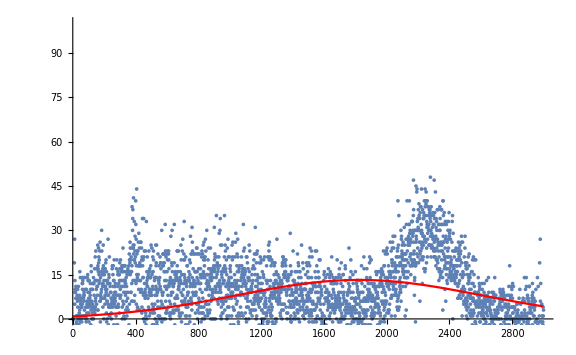

```mathematica
min=1;
max=3000;
guessCenter=1600;
g1=ListPlot[data4⟦min;;max⟧,PlotRange->{0,100},ImageSize->Large];
nlm=NonlinearModelFit[data4,A1 Exp[-(x-A2)^2/(2 A3^2)],{{A1},{A2,guessCenter},{A3}},x]
Print[nlm["BestFitParameters"]];
{A1,A2,A3}={A1,A2,A3}//.nlm["BestFitParameters"];
g2  = Plot[nlm[t],{t,0,max-min},PlotStyle->Red,PlotRange->All];
Show[g1,g2]
```

#### Finding Conversion Factor

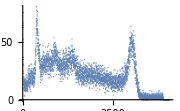

FittedModel[61.4052 ⅇ^(-0.000150125 (-107.444+x)^2)]

{A11→61.4052,A22→107.444,A33→57.7111}

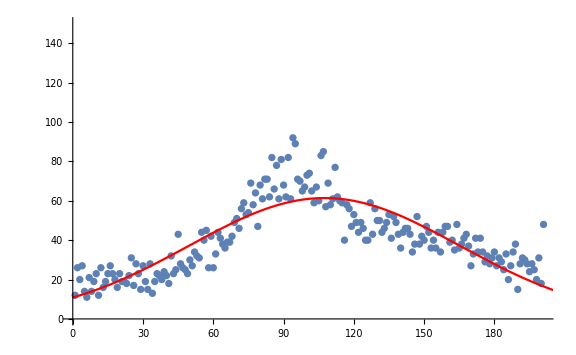

```mathematica
min2=300;
max2=500;
guessCenter2=100;
ListPlot[data3a,ImageSize->Small]
g11=ListPlot[data3a⟦min2;;max2⟧,PlotRange->{0,150},ImageSize->Large];
nlm2=NonlinearModelFit[data3a⟦min2;;max2⟧,A11 Exp[-(x-A22)^2/(2 A33^2)],{{A11},{A22,guessCenter2},{A33}},x]
Print[nlm2["BestFitParameters"]];
g22  = Plot[nlm2[t],{t,0,max-min},PlotStyle->Red,PlotRange->All];
Show[g11,g22]
```